# Quantica

## Calculator of quantum systems with mathematica

20 December, 2013

## Systems

よく使う系の定義集

```mathematica
Exit[]
```

```mathematica
Get["Quantica`Systems`"]
Names["Systems`*"]
```

{Systems`DoubleWell,Systems`Harmonic,Systems`Henon,Systems`JeremyNormal,Systems`JeremyNormal2,Systems`LinearRotor,Systems`LogCoshRotor,Systems`Pendulum,Systems`Standard}

### 調和振動子

```mathematica
Clear[ω]
{T,V}=Systems`Harmonic[ω];
{T[p],V[q]}
```

{p^2/2,(q^2 ω)/2}

#### 等エネルギー面

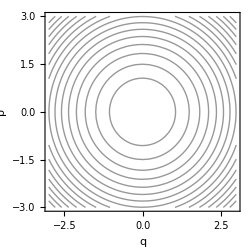

```mathematica
ω=1;
H[q_,p_] := T[p] + V[q]
ContourPlot[H[q,p],{q,-3,3},{p,-3,3},Contours->15,ContourShading->None,Axes->True,FrameLabel->{"q","p"},ImageSize->{250,250}]
```

### Henon

```mathematica
Clear[ϵ]
{T,V} = Systems`Henon[ϵ];
{T[p],V[q]}
```

{p^2/2,(2 q^2+q^3/3) ϵ}

#### 等エネルギー面

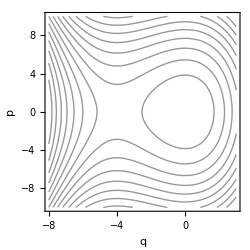

```mathematica
ϵ=1;
H[q_,p_] := T[p] + V[q]
ContourPlot[H[q,p],{q,-8,3},{p,-10,10},Contours->15,ContourShading->None,Axes->True,FrameLabel->{"q","p"},ImageSize->{250,250}]
```

### Double well

```mathematica
Clear[a];
{T,V}=Systems`DoubleWell[a];
{T[p],V[q]}
```

{p^2/2,(-a^2+q^2)^2}

#### 等エネルギー面

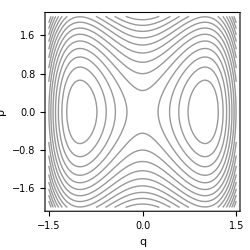

```mathematica
a=1;
H[q_,p_] := T[p] + V[q]
ContourPlot[H[q,p],{q,-3/2,3/2},{p,-2,2},Contours->15,ContourShading->None,Axes->True,FrameLabel->{"q","p"},ImageSize->{250,250}]
```

### Pendulum

```mathematica
Clear[k]
{T,V} = Systems`Pendulum[k];
{T[p],V[q]}
```

{p^2/2,k Cos[q]}

#### 等エネルギー面

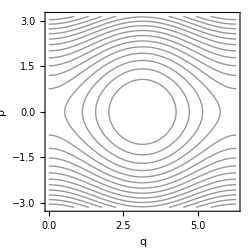

```mathematica
k=1;
H[q_,p_] := T[p] + V[q]
ContourPlot[H[q,p],{q,0,2*Pi},{p,-Pi,Pi},Contours->15,ContourShading->None,Axes->True,FrameLabel->{"q","p"},ImageSize->{250,250}]
```

### 標準写像

```mathematica
Clear[k]
{T,V}=Systems`Standard[k];
{T[p],V[q]}
```

{p^2/2,(k Cos[2 π q])/(4 π^2)}

#### 等エネルギー面

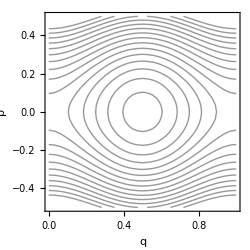

```mathematica
k=1;
H[q_,p_] := T[p] + V[q]
ContourPlot[H[q,p],{q,0,1},{p,-1/2,1/2},Contours->15,ContourShading->None,Axes->True,FrameLabel->{"q","p"},ImageSize->{250,250}]
```

### Linear Rotor

```mathematica
Clear[k,ω]
{T,V}=Systems`LinearRotor[k,ω];
{T[p],V[q]}
```

{p ω,(k Cos[2 π q])/(4 π^2)}

#### 等エネルギー面

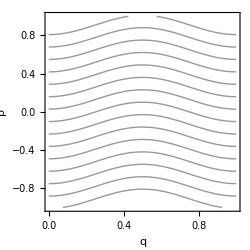

```mathematica
k=4;ω=1;
H[q_,p_] := T[p] + V[q]
ContourPlot[H[q,p],{q,0,1},{p,-1,1},Contours->15,ContourShading->None,Axes->True,FrameLabel->{"q","p"},ImageSize->{250,250}]
```

### LogCosh Rotor

```mathematica
Clear[k,ω,β]
{T,V}=Systems`LogCoshRotor[k,ω,β];
{T[p],V[q]}
```

{p/2+p ω+Log[Cosh[p β]]/(2 β),(k Cos[2 π q])/(4 π^2)}

#### 等エネルギー面

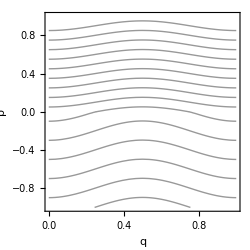

```mathematica
k=4;ω=1;β=100;
H[q_,p_] := T[p] + V[q]
ContourPlot[H[q,p],{q,0,1},{p,-1,1},Contours->15,ContourShading->None,Axes->True,FrameLabel->{"q","p"},ImageSize->{250,250}]
```

### Jérémy Normal form system

この論文1で用いられてい系は

```mathematica
Clear[a1,a2,b,phi,ϕ]
{T,V}=Systems`JeremyNormal[a1->a1,a2->a2,b->b,phi->ϕ] ;
```

```mathematica
T[q,p]
```

1/2 a1 (Cos[p]^2+Cos[q]^2)+a2 (Cos[p]^2+Cos[q]^2)^2

```mathematica
V[q,p]
```

Abs[b] ((Cos[p]^4-6 Cos[p]^2 Cos[q]^2+Cos[q]^4) Cos[ϕ]-4 (Cos[p]^3 Cos[q]-Cos[p] Cos[q]^3) Sin[ϕ])

である．

```mathematica
H[q_,p_] := T[q,p] + V[q,p]
D[H[q,p], q]
```

-a1 Cos[q] Sin[q]-4 a2 Cos[q] (Cos[p]^2+Cos[q]^2) Sin[q]+Abs[b] (Cos[ϕ] (12 Cos[p]^2 Cos[q] Sin[q]-4 Cos[q]^3 Sin[q])-4 (-Cos[p]^3 Sin[q]+3 Cos[p] Cos[q]^2 Sin[q]) Sin[ϕ])

```mathematica
D[H[q,p], p]
```

-a1 Cos[p] Sin[p]-4 a2 Cos[p] (Cos[p]^2+Cos[q]^2) Sin[p]+Abs[b] (Cos[ϕ] (-4 Cos[p]^3 Sin[p]+12 Cos[p] Cos[q]^2 Sin[p])-4 (-3 Cos[p]^2 Cos[q] Sin[p]+Cos[q]^3 Sin[p]) Sin[ϕ])

#### 等エネルギー面

論文のFig. 2 に対応する等エネルギー面を書いてみよう．Systems`JeremyNormal関数のデフォルトパラメーターは論文のFig .2 と同じにしている．

```mathematica
Options[Systems`JeremyNormal]
```

{Systems`Private`a1→1,Systems`Private`a2→-11/20,Systems`Private`b→1/20,Systems`Private`phi→0}

```mathematica
philist={0,Pi/4,Pi/2,Pi};
sys = Systems`JeremyNormal[phi->#1] & /@philist;
```

```mathematica
Table[{T,V} = sys[[i]];
H[q_,p_] := T[q,p]+V[q,p];
ContourPlot[H[q,p],{q,-Pi,Pi},{p,-Pi,Pi},Contours->Range[-0.15,0.15,0.02],ImageSize->{250,250},ContourShading->Automatic,ColorFunction->"LakeColors",PlotLegends->Automatic],
{i,1,Length[sys]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

論文で非線形共鳴の井戸はそんなに深そうに見えないが，実は結構深い事が分かる．共鳴のエネルギー面は低くなってるんじゃなくて，高くなっている(丘上構造)．

{-Graphics-}

## Reference

1	J. L. Deunff, and A. Mouchet, P. Schlagheck, Phys.l Rev E, 88, 042927, (2013)